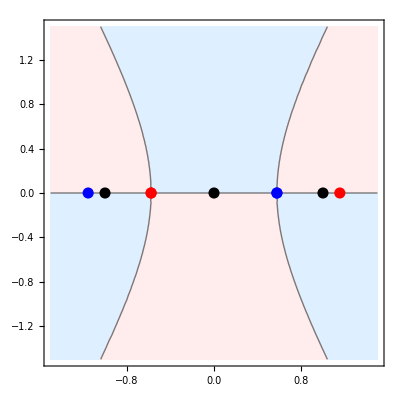

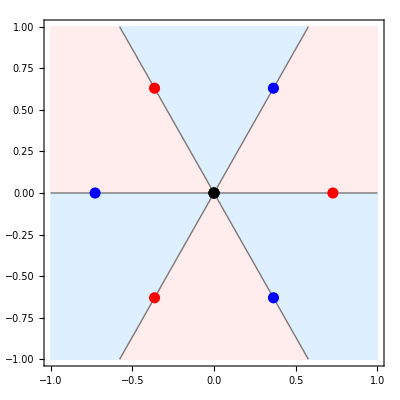

```mathematica
c=2/Sqrt[27];
diag=1+I;
size=PointSize[0.02];
proc[f_,a_,b_]:=Module[{cp,lp1,lp2,lp3,z1,z2,z3},
z1=z/.Solve[f==0];
z2=z/.Solve[f==c];
z3=z/.Solve[f==-c];
cp=ComplexContourPlot[16Im[f],{z,a-b*diag,a+b*diag},Contours->{0},ContourShading->{LightBlue,LightPink}];
lp1=ComplexListPlot[z1,PlotStyle->{Black,size}];
lp2=ComplexListPlot[z2,PlotStyle->{Red,size}];
lp3=ComplexListPlot[z3,PlotStyle->{Blue,size}];
Show[cp,lp1,lp2,lp3]];
pz=proc[z^3-z,0,3/2]
pw=proc[z^3,0,1]
```